## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PGCD";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)


(* user will need to change this path *)
pathMASSef = "C:/MASSef/";
kineticDataFileName =  "kinetic_data.csv";

mainFolder = "fit_PGCD_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:C:\MASSef\examples\

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName,  assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{3pg,Km or S05 substrate}

{0.0012,Km or S05 value}

{{{3pg,Null}},kcat substrates}

{0.55,kcat value}

{3pg,Other parameter susbtrate}

{183,Other parameter value}

{3pg,Other parameter susbtrate}

{3.8×10^-6,Other parameter value}

{3php,Km or S05 substrate}

{3.2×10^-6,Km or S05 value}

{{{3php,Null}},kcat substrates}

{27.8,kcat value}

{3php,Other parameter susbtrate}

{9270,Other parameter value}

{3pg,Km or S05 substrate}

{0.00049,Km or S05 value}

{{{3pg,Null}},kcat substrates}

{13.5,kcat value}

{3pg,Other parameter susbtrate}

{4610,Other parameter value}

{nadh,Km or S05 substrate}

{0.00012,Km or S05 value}

{3php,Km or S05 substrate}

{0.00035,Km or S05 value}

{3pg,Km or S05 substrate}

{0.00119,Km or S05 value}

{nad,Km or S05 substrate}

{0.00001,Km or S05 value}

{nad,Null;3pg,Null;,Keq substrate}

{3.9×10^-6,Keq value}

((3pg)^c+nad^c⇌(3php)^c+nadh^c)^PGCD

Null;

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nad,Null;3pg,Null; | 3.9×10^-6 | 3.705×10^-6
4.095×10^-6 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | 0.0012 | 0.00114
0.00126 | nad | 0.001 | M | 8.8 | 37 | trishcl | 0.04 | 
1 | 3php | 3.2×10^-6 | 3.04×10^-6
3.36×10^-6 | nadh | 0.00025 | M | 7.5 | 37 | kpi | 0.04 | 
1 | 3pg | 0.00049 | 0.00046
0.00052 | nadh | 0.00025 | M | 7.5 |  | kpi | 0.02 | 
1 | nadh | 0.00012 | 0.000114
0.000126 | 3php | 0.00009 | M | 7.1 | 30 | hepes | 0.025 | k | 0.0004
cl | 0.0004
1 | 3php | 0.00035 | 0.0003325
0.0003675 | nadh | 0.0001 | M | 7.1 | 30 | hepes | 0.025 | k | 0.0004
cl | 0.0004
1 | 3pg | 0.00119 | 0.0011305
0.0012495 | nad | 0.0005 | M | 9 | 30 | trishcl | 0.02 | 
1 | nad | 0.00001 | 9.5×10^-6
0.0000105 | 3pg | 0.005 | M | 9 | 30 | trishcl | 0.02 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null | 0.55 | 0.5225
0.5775 | 1/s | 8.8 | 37 | trishcl | 0.04 | 
1 | 3php | Null | 27.8 | 26.41
29.19 | 1/s | 7.5 | 37 | kpi | 0.04 | 
1 | 3pg | Null | 13.5 2.5^(0.1 (37-)) | 12.825 2.5^(0.1 (37-))
14.175 2.5^(0.1 (37-)) | 1/s | 7.5 | 37 | kpi | 0.02 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | vmax | 3pg | 183 | 173.85
192.15 | nad | 0.001 | U/mg | 8.8 | 37 | trishcl | 0.04 | 
1 | Kicu | 3pg | 3.8×10^-6 | 3.61×10^-6
3.99×10^-6 | nad | 0.001 | M | 8.8 | 37 | trishcl | 0.04 | 
1 | vmax | 3php | 9270 | 8806.5
9733.5 | nadh | 0.00025 | U/mg | 7.5 | 37 | kpi | 0.04 | 
1 | vmax | 3pg | 4610 | 4550.
4670 | nadh | 0.00025 | U/mg | 7.5 |  | kpi | 0.02 |

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)


KeqPriorities = {1};
kmPriorities = {0,0,0,1,1,1,1};
s05Priorities = Null;
kcatPriorities = {1,0,0};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = {0,0,0,0};

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((3pg)^c+nad^c⇌(3php)^c+nadh^c)^PGCD

Null;

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nad,Null;3pg,Null; | 3.9×10^-6 | 3.705×10^-6
4.095×10^-6 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nadh | 0.00012 | 0.000114
0.000126 | 3php | 0.00009 | M | 7.1 | 30 | hepes | 0.025 | k | 0.0004
cl | 0.0004
1 | 3php | 0.00035 | 0.0003325
0.0003675 | nadh | 0.0001 | M | 7.1 | 30 | hepes | 0.025 | k | 0.0004
cl | 0.0004
1 | 3pg | 0.00119 | 0.0011305
0.0012495 | nad | 0.0005 | M | 9 | 30 | trishcl | 0.02 | 
1 | nad | 0.00001 | 9.5×10^-6
0.0000105 | 3pg | 0.005 | M | 9 | 30 | trishcl | 0.02 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null | 0.55 | 0.5225
0.5775 | 1/s | 8.8 | 37 | trishcl | 0.04 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_PGCD[c] + 3pg[c] <=> E_PGCD[c]&3pg",
				"E_PGCD[c]&3pg + nad[c] <=> E_PGCD[c]&3pg&nad",
				"E_PGCD[c]&3pg&nad <=> E_PGCD[c]&3php&nadh",
				"E_PGCD[c]&3php&nadh <=> E_PGCD[c]&3php + nadh[c]",
				"E_PGCD[c]&3php <=> E_PGCD[c] + 3php[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((PGCD^c)_^+(3pg)^c⇌(PGCD^c&(3pg)^c)_^)^PGCD1,((PGCD^c&(3php)^c)_^⇌(PGCD^c)_^+(3php)^c)^PGCD2,((PGCD^c&(3pg)^c)_^+nad^c⇌(PGCD^c&(3pg)^c&nad^c)_^)^PGCD3,((PGCD^c&(3php)^c&nadh^c)_^⇌(PGCD^c&(3php)^c)_^+nadh^c)^PGCD4,((PGCD^c&(3pg)^c&nad^c)_^⇌(PGCD^c&(3php)^c&nadh^c)_^)^PGCD5}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PGCD^c)_^+(3pg)^c⇌(PGCD^c&(3pg)^c)_^)^PGCD1,Overscript[(PGCD^c&(3php)^c)_^⇌(PGCD^c)_^+(3php)^c, PGCD2],((PGCD^c&(3pg)^c)_^+nad^c⇌(PGCD^c&(3pg)^c&nad^c)_^)^PGCD3,Overscript[(PGCD^c&(3php)^c&nadh^c)_^⇌(PGCD^c&(3php)^c)_^+nadh^c, PGCD4],((PGCD^c&(3pg)^c&nad^c)_^⇌(PGCD^c&(3php)^c&nadh^c)_^)^PGCD5};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=300;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{(3pg)^c→0,nad^c→0}

{(3php)^c→0,nadh^c→0}

{(3pg)^c→∞,nad^c→∞}

{(3php)^c→∞,nadh^c→∞}

Added inhibition reactions:

{}

Generating flux equation...

{((PGCD^c&(3pg)^c&nad^c)_^-((PGCD^c&(3php)^c&nadh^c)_^)/K_PGCD5) Volume_c k_PGCD5^⟶}

Volume_c (-(PGCD^c&(3php)^c&nadh^c)_^ k_PGCD5^⟵+(PGCD^c&(3pg)^c&nad^c)_^ k_PGCD5^⟶)

1

2

3

0.230643

4

0.0009711

5

0.

Simplifying...

6

0.108759

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	3pg[c]	3php[c]	nad[c]	nadh[c]	param_PGCD_total	param_pH	param_Temp	FileFlag	Target_Data

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
0.7	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
0.7	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
0.7	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
0.7	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
0.7	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
0.7	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
0.7	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
0.7	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
0.7	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
0.7	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
0.7	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
0.7	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
0.7	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
0.7	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
0.7	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
0.7	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
0.7	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
0.7	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
0.7	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
0.7	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
0.7	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
0.7	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	10
filesWithFunctions	[C:\MASSef\examples\fit_PGCD_typeII\input\absRateFor.txt, C:\MASSef\examples\fit_PGCD_typeII\input\absRateRev.txt, C:\MASSef\examples\fit_PGCD_typeII\input\relRateFor_3pg.txt, C:\MASSef\examples\fit_PGCD_typeII\input\relRateFor_nad.txt, C:\MASSef\examples\fit_PGCD_typeII\input\relRateRev_3php.txt, C:\MASSef\examples\fit_PGCD_typeII\input\relRateRev_nadh.txt, C:\MASSef\examples\fit_PGCD_typeII\input\haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	10
filesWithFunctions	[C:\MASSef\examples\fit_PGCD_typeII\input\absRateFor.txt, C:\MASSef\examples\fit_PGCD_typeII\input\absRateRev.txt, C:\MASSef\examples\fit_PGCD_typeII\input\relRateFor_3pg.txt, C:\MASSef\examples\fit_PGCD_typeII\input\relRateFor_nad.txt, C:\MASSef\examples\fit_PGCD_typeII\input\relRateRev_3php.txt, C:\MASSef\examples\fit_PGCD_typeII\input\relRateRev_nadh.txt, C:\MASSef\examples\fit_PGCD_typeII\input\haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 2.95693160044
best_fit: 2.29044424484
best_fit: 5.91399948055
best_fit: 2.95680440138
best_fit: 2.95705596855

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 3.02782 | 9.16769 | 0.00415409 | 106515. | 3.9×10^-6 | 0.00415799
1 | haldaneRatio_1 | 3.02782 | 9.16769 | 0.00415409 | 106515. | 3.9×10^-6 | 0.00415799
1 | haldaneRatio_1 | 3.02782 | 9.16769 | 0.00415409 | 106515. | 3.9×10^-6 | 0.00415799
1 | haldaneRatio_1 | 3.02782 | 9.16769 | 0.00415409 | 106515. | 3.9×10^-6 | 0.00415799
1 | haldaneRatio_1 | 3.02782 | 9.16769 | 0.00415409 | 106515. | 3.9×10^-6 | 0.00415799
1 | haldaneRatio_1 | 3.02782 | 9.16769 | 0.00415409 | 106515. | 3.9×10^-6 | 0.00415799
1 | haldaneRatio_1 | 3.02782 | 9.16769 | 0.00415409 | 106515. | 3.9×10^-6 | 0.00415799
1 | haldaneRatio_1 | 3.02782 | 9.16769 | 0.00415409 | 106515. | 3.9×10^-6 | 0.00415799
1 | haldaneRatio_1 | 3.02782 | 9.16769 | 0.00415409 | 106515. | 3.9×10^-6 | 0.00415799
1 | haldaneRatio_1 | 3.02782 | 9.16769 | 0.00415409 | 106515. | 3.9×10^-6 | 0.00415799
1 | haldaneRatio_1 | 3.02782 | 9.16769 | 0.00415409 | 106515. | 3.9×10^-6 | 0.00415799
1 | relRateRev_nadh | 0.000161719 | 2.6153×10^-8 | 0.0000338583 | 0.0372441 | 0.0909091 | 0.0909429
1 | relRateRev_nadh | 0.000153553 | 2.35784×10^-8 | 0.0000483791 | 0.0353631 | 0.136807 | 0.136855
1 | relRateRev_nadh | 0.000142174 | 2.02135×10^-8 | 0.0000657333 | 0.0327422 | 0.20076 | 0.200826
1 | relRateRev_nadh | 0.000127232 | 1.6188×10^-8 | 0.0000834324 | 0.0293005 | 0.284747 | 0.284831
1 | relRateRev_nadh | 0.000109065 | 1.18951×10^-8 | 0.0000971656 | 0.0251163 | 0.386863 | 0.38696
1 | relRateRev_nadh | 0.000088938 | 7.90997×10^-9 | 0.000102404 | 0.0204808 | 0.5 | 0.500102
1 | relRateRev_nadh | 0.0000688121 | 4.7351×10^-9 | 0.0000971566 | 0.0158458 | 0.613137 | 0.613234
1 | relRateRev_nadh | 0.0000506475 | 2.56517×10^-9 | 0.0000834177 | 0.0116627 | 0.715253 | 0.715336
1 | relRateRev_nadh | 0.0000357082 | 1.27508×10^-9 | 0.0000657171 | 0.00822245 | 0.79924 | 0.799306
1 | relRateRev_nadh | 0.0000243328 | 5.92088×10^-10 | 0.0000483647 | 0.005603 | 0.863193 | 0.863241
1 | relRateRev_nadh | 0.0000161692 | 2.61443×10^-10 | 0.0000338469 | 0.00372316 | 0.909091 | 0.909125
1 | relRateRev_3php | 0.000199436 | 3.97745×10^-8 | 0.0000417566 | 0.0459323 | 0.0909091 | 0.0909508
1 | relRateRev_3php | 0.000189364 | 3.58588×10^-8 | 0.0000596646 | 0.0436123 | 0.136807 | 0.136867
1 | relRateRev_3php | 0.000175332 | 3.07412×10^-8 | 0.0000810664 | 0.0403798 | 0.20076 | 0.200841
1 | relRateRev_3php | 0.000156904 | 2.46188×10^-8 | 0.000102893 | 0.036135 | 0.284747 | 0.28485
1 | relRateRev_3php | 0.000134499 | 1.80901×10^-8 | 0.000119829 | 0.0309744 | 0.386863 | 0.386983
1 | relRateRev_3php | 0.000109678 | 1.20293×10^-8 | 0.000126288 | 0.0252575 | 0.5 | 0.500126
1 | relRateRev_3php | 0.0000848585 | 7.20096×10^-9 | 0.000119815 | 0.0195413 | 0.613137 | 0.613257
1 | relRateRev_3php | 0.0000624577 | 3.90097×10^-9 | 0.000102871 | 0.0143825 | 0.715253 | 0.715356
1 | relRateRev_3php | 0.0000440347 | 1.93905×10^-9 | 0.0000810419 | 0.0101399 | 0.79924 | 0.799321
1 | relRateRev_3php | 0.0000300067 | 9.00403×10^-10 | 0.0000596427 | 0.00690954 | 0.863193 | 0.863253
1 | relRateRev_3php | 0.0000199394 | 3.97581×10^-10 | 0.0000417394 | 0.00459133 | 0.909091 | 0.909133
1 | relRateFor_3pg | 0.0000659434 | 4.34853×10^-9 | 0.0000138026 | 0.0151829 | 0.0909091 | 0.0908953
1 | relRateFor_3pg | 0.0000626143 | 3.92055×10^-9 | 0.0000197227 | 0.0144164 | 0.136807 | 0.136787
1 | relRateFor_3pg | 0.0000579756 | 3.36117×10^-9 | 0.0000267984 | 0.0133485 | 0.20076 | 0.200733
1 | relRateFor_3pg | 0.0000518836 | 2.69191×10^-9 | 0.0000340157 | 0.0119459 | 0.284747 | 0.284713
1 | relRateFor_3pg | 0.0000444766 | 1.97817×10^-9 | 0.0000396171 | 0.0102406 | 0.386863 | 0.386824
1 | relRateFor_3pg | 0.0000362701 | 1.31552×10^-9 | 0.0000417557 | 0.00835115 | 0.5 | 0.499958
1 | relRateFor_3pg | 0.0000280634 | 7.87554×10^-10 | 0.0000396186 | 0.00646162 | 0.613137 | 0.613097
1 | relRateFor_3pg | 0.000020656 | 4.2667×10^-10 | 0.0000340182 | 0.0047561 | 0.715253 | 0.715219
1 | relRateFor_3pg | 0.0000145635 | 2.12096×10^-10 | 0.0000268011 | 0.00335332 | 0.79924 | 0.799213
1 | relRateFor_3pg | 9.9243×10^-6 | 9.84917×10^-11 | 0.0000197251 | 0.00228513 | 0.863193 | 0.863173
1 | relRateFor_3pg | 6.59479×10^-6 | 4.34912×10^-11 | 0.0000138045 | 0.00151849 | 0.909091 | 0.909077
1 | relRateFor_nad | 0.00107325 | 1.15186×10^-6 | 0.000224381 | 0.246819 | 0.0909091 | 0.0906847
1 | relRateFor_nad | 0.00101912 | 1.03861×10^-6 | 0.000320658 | 0.234387 | 0.136807 | 0.136486
1 | relRateFor_nad | 0.000943701 | 8.90571×10^-7 | 0.000435768 | 0.217059 | 0.20076 | 0.200324
1 | relRateFor_nad | 0.000844629 | 7.13399×10^-7 | 0.000553247 | 0.194294 | 0.284747 | 0.284194
1 | relRateFor_nad | 0.000724143 | 5.24383×10^-7 | 0.000644518 | 0.166601 | 0.386863 | 0.386219
1 | relRateFor_nad | 0.000590614 | 3.48825×10^-7 | 0.000679507 | 0.135901 | 0.5 | 0.49932
1 | relRateFor_nad | 0.000457044 | 2.08889×10^-7 | 0.000644915 | 0.105183 | 0.613137 | 0.612492
1 | relRateFor_nad | 0.00033645 | 1.13198×10^-7 | 0.000553895 | 0.0774404 | 0.715253 | 0.714699
1 | relRateFor_nad | 0.00023724 | 5.62827×10^-8 | 0.000436477 | 0.0546116 | 0.79924 | 0.798804
1 | relRateFor_nad | 0.00016168 | 2.61404×10^-8 | 0.000321291 | 0.0372212 | 0.863193 | 0.862872
1 | relRateFor_nad | 0.000107444 | 1.15442×10^-8 | 0.000224881 | 0.0247369 | 0.909091 | 0.908866
1 | absRateFor | 0.000026411 | 6.97539×10^-10 | 0.0000334464 | 0.00608116 | 0.55 | 0.549967
1 | absRateFor | 0.000026411 | 6.97539×10^-10 | 0.0000334464 | 0.00608116 | 0.55 | 0.549967
1 | absRateFor | 0.000026411 | 6.97539×10^-10 | 0.0000334464 | 0.00608116 | 0.55 | 0.549967
1 | absRateFor | 0.000026411 | 6.97539×10^-10 | 0.0000334464 | 0.00608116 | 0.55 | 0.549967
1 | absRateFor | 0.000026411 | 6.97539×10^-10 | 0.0000334464 | 0.00608116 | 0.55 | 0.549967
1 | absRateFor | 0.000026411 | 6.97539×10^-10 | 0.0000334464 | 0.00608116 | 0.55 | 0.549967
1 | absRateFor | 0.000026411 | 6.97539×10^-10 | 0.0000334464 | 0.00608116 | 0.55 | 0.549967
1 | absRateFor | 0.000026411 | 6.97539×10^-10 | 0.0000334464 | 0.00608116 | 0.55 | 0.549967
1 | absRateFor | 0.000026411 | 6.97539×10^-10 | 0.0000334464 | 0.00608116 | 0.55 | 0.549967
1 | absRateFor | 0.000026411 | 6.97539×10^-10 | 0.0000334464 | 0.00608116 | 0.55 | 0.549967
1 | absRateFor | 0.000026411 | 6.97539×10^-10 | 0.0000334464 | 0.00608116 | 0.55 | 0.549967

### Simulated Data and Best Fit Data Plot

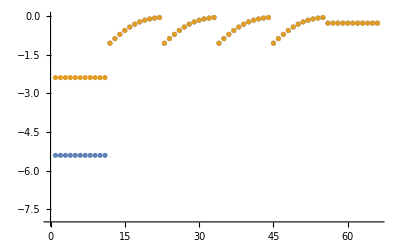

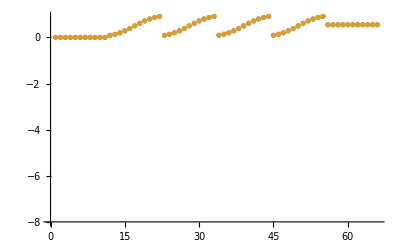

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

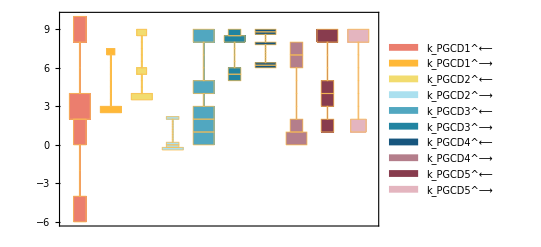

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

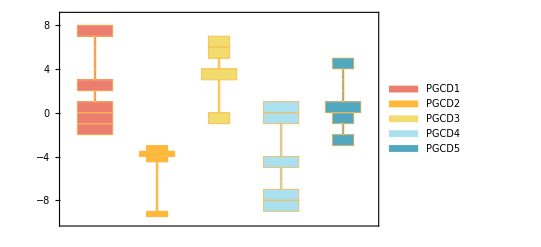

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

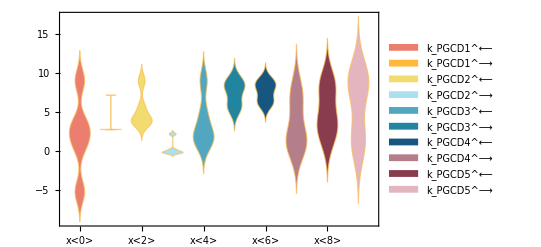

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```



```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.000045 | 2.51272×10^-6
0.00089 | 0.00089 | 1.39821×10^-6
0.00053 | 0.00053 | 1.35758×10^-6

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 3.33383×10^-6

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 8.29398×10^-6

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.452 | 0.452 | 4.57492×10^-6